## Atomic to Physical Unit Conversions

```mathematica
(* Converting Atomic Units into Lab Units *)
Module[{enAU,enAU1GHz,tAU,tAU1ns,fAU,fAU1mVcm},
(* 1 GHz below ZFIP in AU *)
enAU=Quantity[4.35974417*10^-18,"Joules"];
enAU1GHz=UnitConvert[Quantity["PlanckConstant"]*Quantity[1,"Gigahertz"]/enAU];
Print["1 GHz Photon Energy = ",enAU1GHz, " A.U."];

(* 1 ns in AU *)
tAU=Quantity[2.418884326505*10^-17,"Seconds"];
tAU1ns=UnitConvert[Quantity[1,"nanosecond"]/tAU];
Print["1 ns = ",tAU1ns, " A.U."];

(* 1 mV/cm in AU *)
fAU=Quantity[5.14220652*10^11,"Volts"/"Meters"];
fAU1mVcm=UnitConvert[Quantity[1,"Millivolts"/"Centimeters"]/fAU];
Print["1 mV/cm = ",fAU1mVcm," A.U."];

(* Association *)
au=Association[{"GHz"->enAU1GHz,"ns"->tAU1ns,"mVcm"->fAU1mVcm}]
];
```

1 GHz Photon Energy = 1.51983×10^-7 A.U.

1 ns = 4.13414×10^7 A.U.

1 mV/cm = 1.94469×10^-13 A.U.

```mathematica
au["GHz"]
au["ns"]
au["mVcm"]
```

1.51983×10^-7

4.13414×10^7

1.94469×10^-13

```mathematica
Module[{f,ω},
f=4*1000*au["mVcm"];
ω=15.932*10^9*2*π/au["ns"];
Print[(3/2*f/ω^(2/3))/au["GHz"]]
]
```

0.0000425758

## Solver and Helper Functions

```mathematica
solver=Function[
{ic,fields,timing}, (* ic, fields, timing *)
(* A solver based only on initial conditions,physical conditions and start and stop times. *)
Module[{sol,x0,z0,vx0,vz0,fpulse,fmw,ω,α,toff,τring,t0,tmax},
ClearAll[x,z,t];
(* Unpack *)
{x0,z0,vx0,vz0}=ic;
{fpulse,fmw,ω,α}=fields;
{toff,τring,t0,tmax}=timing;
(* solve *)
sol=NDSolve[
{
x''[t]==-x[t]/(x[t]^2+z[t]^2)^(3/2), (* -r/r^3 *)
x'[t0]==vx0,
x[t0]==x0,
z''[t]==-z[t]/(x[t]^2+z[t]^2)^(3/2) (* -r/r^3 *)
-fpulse*If[t<toff,1,0] (* Field that switches off *)
-fmw*Sin[ω*t+α]*If[t<toff,1,E^(-(t-toff)/τring)], (* MW that rings down *)
z'[t0]==vz0,
z[t0]==z0
},
{x,z},{t,t0,tmax},AccuracyGoal->13,PrecisionGoal->13,MaxSteps->1000000
];
(* return *)
sol]
];

icstarting=Function[
{w0,l0,θLRL,dL},
(* For starting the simulation with known energy, angular momentum, orientation, and angular momentum direction *)
(* r0 and v0 from initial energy *)
If[w0==0,
r0=l0^2/2;
v0=2/l0;
,
r0=(-1+√(1+2*w0*l0^2))/(2*w0);
v0=(1+√(1+2*w0*l0^2))/l0;
];
(* Orient r and v based on θLRL and dL *)
x0=r0*Sin[θLRL];
z0=-r0*Cos[θLRL];
vx0=dL*v0*Cos[θLRL];
vz0=dL*v0*Sin[θLRL];
{x0,z0,vx0,vz0}];

icskip=Function[
{bc,fields,timing,ts,θLRL},
Module[{xf,zf,vxf,vzf,fpulse,fmw,ω,α,toff,τring,t0,tmax,xi,zi,wf,Δw,wi,θvf,vi,vxi,vzi},
(* Unpack *)
{xf,zf,vxf,vzf}=bc;
{fpulse,fmw,ω,α}=fields;
{toff,τring,t0,tmax}=timing;
(* Position *)
xi=xf;
zi=zf;
(* Energy *)
wf=wfunc[xf,zf,vxf,vzf];
Δw=wslingshot[ts,fields,timing,θLRL];
wi=wf+Δw;
(* Velocity *)
θvf=ArcTan[vxf,vzf];
(* If there's not enough energy, vi=0 and scale ri *)
If[wi+1/rfunc[xi,zi]>0,
vi=√(2*(wi+1/rfunc[xi,zi]));
,
vi=0;
rscale=(-1/wi)/rfunc[xi,zi];
xi=xi*rscale;
zi=zi*rscale;
];
{vxi,vzi}={vi*Cos[θvf+π],vi*Sin[θvf+π]};
{xi,zi,vxi,vzi}]
];

timeskip=Function[{sol,fields},
Module[{ts,fpulse,fmw,ω,α},
(* Unpack *)
{fpulse,fmw,ω,α}=fields;
ts=sol[[1,2]]["Domain"][[1,2]];
qr=QuotientRemainder[ts*ω+α+π/2,π]; (* Q is # of periods, R is radians away from ϕ=0 *)
tminus=ts-(2π+qr[[2]])/ω;
tplus=ts+(2π+(π-qr[[2]]))/ω;
{ts,tminus,tplus}]
];

fcskip=Function[{sol,tfinal},
Module[{xf,zf,vxf,vzf},
xf=x[tfinal]/.sol;
zf=z[tfinal]/.sol;
vxf=x'[tfinal]/.sol;
vzf=z'[tfinal]/.sol;
{xf,zf,vxf,vzf}]
];

geterror=Function[{soldata,fields},
Module[{errmess,sol,suc,err,ts,tminus,tplus,tlims},
sol=soldata["Result"][[1]];
suc=soldata["Success"];
err=If[suc==False,soldata["MessagesExpressions"][[1,1,1,2]]];
errmess=Which[
suc==True,"NOERR",
(* mxst *)
(suc==False)&&(err=="mxst"),err,
(* ndsz *)
(suc==False)&&(err=="ndsz"),
{ts,tminus,tplus}=timeskip[sol,fields];
tlims=sol[[1,2]]["Domain"][[1]];
If[tminus>tlims[[1]],err,"ShortOrb"],
(* Other *)
True,"UNKN"
];
(* return *)
errmess]
];

iterndsz=Function[{soldata,fields,timing,θLRL},
Module[{toff,τring,t0,tmax,sol,tlims,ts,tminus,tplus,timing2,bc,ic,soldata2},
{toff,τring,t0,tmax}=timing;
sol=soldata["Result"][[1]];
tlims=sol[[1,2]]["Domain"][[1]];
{ts,tminus,tplus}=timeskip[sol,fields];
(* Timing *)
timing2=Join[timing[[{1,2}]],{tplus,tmax}];
(* Translate Initial Conditions *)
bc=fcskip[sol,tminus];
ic=icskip[bc,fields,timing2,ts,θLRL];
(* Second Solution *)
soldata2=EvaluationData[solver[ic,fields,timing2]];
(* return *)
soldata2]
];

itermxst=Function[{soldata,timing,fields},
Module[{toff,τring,t0,tmax,sol,tlims,timing2,ic,soldata2},
{toff,τring,t0,tmax}=timing;
sol=soldata["Result"][[1]];
tlims=sol[[1,2]]["Domain"][[1]];
timing2=Join[timing[[{1,2}]],{tlims[[2]],tmax}];
(* IC *)
ic=fcskip[sol,tlims[[2]]];
(* Solve *)
soldata2=EvaluationData[solver[ic,fields,timing2]];
(* return *)
soldata2]
];

completesolve=Function[{w0,fpulse,θLRL,dL,α},
Module[{lo,fmw,ω,toff,τring,t0,tmax,ic,fields,timing,soldata,solutions,sol,errmess,n},
(* IC, Unchanged Parameters *)
(* Unchanged Parameters *)
l0=√(3*(3+1));
fmw=4*1000*au["mVcm"];
ω=2*π*15.9/au["ns"];
toff=20*au["ns"];
τring=10*au["ns"];
t0=0;
tmax=toff+5*τring;
(* Packaging *)
ic=icstarting[w0,l0,θLRL,dL];
fields={fpulse,fmw,ω,α};
timing={toff,τring,t0,tmax};

(* First Solve *)
soldata=EvaluationData[solver[ic,fields,timing]];
solutions=Append[{},soldata];
(* Pull out solution *)
sol=soldata["Result"][[1]];

(* Check for Error *)
errmess=geterror[soldata,fields];

(* Iterations *)
n=1;
While[(errmess=="ndsz")||(errmess=="mxst"),
n=n+1;(* run counter *)
(* soldata=itermxst[soldata,timing,fields]; *)
soldata=Which[
errmess=="ndsz",iterndsz[soldata,fields,timing,θLRL],
errmess=="mxst",itermxst[soldata,timing,fields]
];
solutions=Append[solutions,soldata];
errmess=geterror[soldata,fields];
];
(* return *)
{solutions,errmess}]
];


getwfinal=Function[{sol,errmess},
Module[{wfinal,tlims},
tlims=sol[[1,2]]["Domain"][[1]];
Which[
(* NOERR *)
errmess=="NOERR",
wfinal=wfunc[x[t],z[t],x'[t],z'[t]]/.Append[sol,t->tlims[[2]]],
(* ShortOrb *)
errmess=="ShortOrb",
wfinal=wfunc[x[t],z[t],x'[t],z'[t]]/.Append[sol,t->Mean[tlims]],
(* Other *)
True,
wfinal=Indeterminate
];
(* return *)
wfinal]
];

displayreport=Function[{solutions,errmess},
Module[{sol,tlims,wfinal,colors,wplots,rplots,skips,soldata},

(* Report *)
sol=solutions[[-1]]["Result"][[1]];
tlims=sol[[1,2]]["Domain"][[1]];
wfinal=getwfinal[sol,errmess];
Print["Runs :\t",Length[solutions],"\nError :\t",errmess,"\nWfinal =\t",wfinal/au["GHz"]," GHz"];

(* Plotting *)
colors={Red,Green,Blue,Cyan,Magenta,Brown,Orange,Pink,Purple};
wplots={};
rplots={};
skips={};
Do[
soldata=solutions[[i]];
sol=soldata["Result"][[1]];
tlims=sol[[1,2]]["Domain"][[1]];
skips=Append[skips,tlims[[2]]];
wplots=Append[
wplots,
Plot[1/au["GHz"]*wfunc[x[ta],z[ta],x'[ta],z'[ta]]/.Append[sol,ta->t*au["ns"]],{t,tlims[[1]]/au["ns"],tlims[[2]]/au["ns"]},PlotStyle->colors[[Mod[i,Length[colors],1]]]]
];
rplots=Append[
rplots,
Plot[rfunc[x[ta],z[ta]]/.Append[sol,ta->t*au["ns"]],{t,tlims[[1]]/au["ns"],tlims[[2]]/au["ns"]},PlotStyle->colors[[Mod[i,Length[colors],1]]]]
];
,{i,1,Length[solutions]}];
Print[Show[wplots,PlotRange->All,GridLines->{skips/au["ns"],{}}]];
Print[Show[rplots,PlotRange->All,GridLines->{skips/au["ns"],{}}]];
(* return *)
wfinal]
];

writereport=Function[{i,w0,fpulse,dL,α,θLRL,errmess,solutions},
Module[{sol,wfinal},
sol=solutions[[-1]]["Result"][[1]];
wfinal=getwfinal[sol,errmess];
(* return *)
{i[[1]],w0,fpulse,dL,N[α],θLRL,errmess,Length[solutions],wfinal}]
];
```

## Evaluation Functions

```mathematica
wfunc=Function[{x,z,vx,vz},
1/2*(vx^2+vz^2)-1/√(x^2+z^2)];
rfunc=Function[{x,z},
√(x^2+z^2)];
lfunc=Function[{x,z,vx,vz},
z*vx-x*vz];
wslingshot=Function[
{t,fields,timing,θLRL},
Module[{fpulse,fmw,ω,α,toff,τring,t0,tmax,Δw},
{fpulse,fmw,ω,α}=fields;
{toff,τring,t0,tmax}=timing;
Δw=-If[t<toff,1,E^(-(t-toff)/τring)]*Cos[θLRL]*√3*3/2*fmw/ω^(2/3)*Cos[ω*t+α];
(* return *)
Δw]
];
```

## Settings

## Test Case 1 with No Field

### Settings

```mathematica
(* IC *)
w0=-28*au["GHz"];
l0=√(3*(3+1));
θLRL=0;
dL=1;
(* Field parameters *)
fpulse=0*0.72*au["mVcm"];
fmw=4*1000*au["mVcm"];
ω=2*π*15.9/au["ns"];
α=4π/6;
(* timing *)
toff=20*au["ns"];
τring=10*au["ns"];
t0=0;
tmax=toff+5*τring;
(* Getting ic for the solver *)
{x0,z0,vx0,vz0}=icstarting[w0,l0,θLRL,dL];
(* Packaging *)
ic={x0,z0,vx0,vz0};
fields={fpulse,fmw,ω,α};
timing={toff,τring,t0,tmax};
```

### Evaluation

```mathematica
soldata=EvaluationData[solver[ic,fields,timing]];
sol=soldata["Result"][[1]];
tlims=sol[[1,2]]["Domain"][[1]];
ts=FindMinimum[rfunc[x[t],z[t]]/.sol,{t,5.95*au["ns"]}][[2,1,2]];
qr=QuotientRemainder[ts*ω+α+π/2,π]; (* Q is # of periods, R is radians away from ϕ=0 *)
tminus=ts-(2π+qr[[2]])/ω;
tplus=ts+(2π+(π-qr[[2]]))/ω;
style={Red,Thick};
wplus=wfunc[x[t],z[t],x'[t],z'[t]]/.Append[sol,t->tplus];
wminus=wfunc[x[t],z[t],x'[t],z'[t]]/.Append[sol,t->tminus];
gridlines={{{ts/au["ns"],style},{ts/au["ns"]-2π/(ω*au["ns"]),style},{tminus/au["ns"],style},{ts/au["ns"]+2π/(ω*au["ns"]),style},{tplus/au["ns"],style}},{{wplus/au["GHz"],style},{wminus/au["GHz"],style}}};
(* First Segment *)
timing1=Join[timing[[{1,2}]],{0,ts}];
soldata1=EvaluationData[solver[ic,fields,timing1]];
sol1=soldata1["Result"][[1]];
(* Timing *)
{ts1,tminus1,tplus1}=timeskip[sol1,fields];
tlims1=sol1[[1,2]]["Domain"][[1]];
(* Translate Initial Conditions *)
(* xf=x[tminus1]/.sol1;
zf=z[tminus1]/.sol1;
vxf=x'[tminus1]/.sol1;
vzf=z'[tminus1]/.sol1;
bc={xf,zf,vxf,vzf}; *)
bc=fcskip[sol1,tminus1];
(* Timing *)
(* ts1=sol1[[1,2]]["Domain"][[1,2]] *)
timing2=Join[timing[[{1,2}]],{tplus1,tmax}];
ic2=icskip[bc,fields,timing2,ts1,θLRL];
soldata2=EvaluationData[solver[ic2,fields,timing2]];
sol2=soldata2["Result"][[1]];
tlims2=sol2[[1,2]]["Domain"][[1]];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

### Plotting

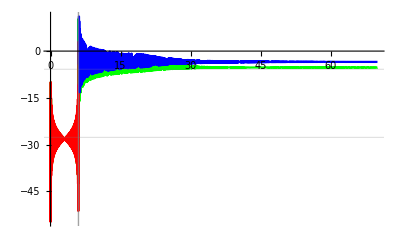

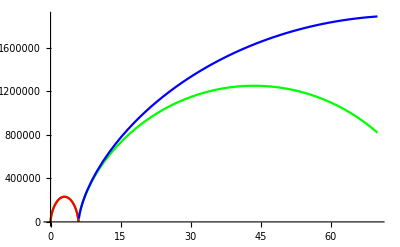

```mathematica
(* Energy *)
Show[
Plot[
(wfunc[x[ta],z[ta],x'[ta],z'[ta]]/.Append[sol,ta->(t*au["ns"])])/au["GHz"],
{t,tlims[[1]]/au["ns"],tlims[[2]]/au["ns"]},PlotRange->All,PlotStyle->Green],
Plot[
(wfunc[x[ta],z[ta],x'[ta],z'[ta]]/.Append[sol1,ta->(t*au["ns"])])/au["GHz"],
{t,tlims1[[1]]/au["ns"],tlims1[[2]]/au["ns"]},PlotRange->All,PlotStyle->Red],
Plot[
(wfunc[x[ta],z[ta],x'[ta],z'[ta]]/.Append[sol2,ta->(t*au["ns"])])/au["GHz"],
{t,tlims2[[1]]/au["ns"],tlims2[[2]]/au["ns"]},PlotRange->All,PlotStyle->Blue](**),
PlotRange->All,GridLines->gridlines]
(* Radius *)
Show[
Plot[rfunc[x[ta],z[ta]]/.Append[sol,ta->t*au["ns"]],{t,tlims[[1]]/au["ns"],tlims[[2]]/au["ns"]},PlotRange->{{tlims[[1]],tlims[[2]]}/au["ns"],All},PlotStyle->Green],Plot[rfunc[x[ta],z[ta]]/.Append[sol1,ta->t*au["ns"]],{t,tlims1[[1]]/au["ns"],tlims1[[2]]/au["ns"]},PlotRange->{{tlims[[1]],tlims[[2]]}/au["ns"],All},PlotStyle->Red],
Plot[rfunc[x[ta],z[ta]]/.Append[sol2,ta->t*au["ns"]],{t,tlims2[[1]]/au["ns"],tlims2[[2]]/au["ns"]},PlotRange->{{tlims[[1]],tlims[[2]]}/au["ns"],All},PlotStyle->Blue]
]
```

## Test Case 2 with No Field

### Settings

```mathematica
(* IC *)
w0=-22*au["GHz"];
l0=√(3*(3+1));
θLRL=π;
dL=-1;
(* Field parameters *)
fpulse=0*0.72*au["mVcm"];
fmw=4*1000*au["mVcm"];
ω=2*π*15.9/au["ns"];
α=4π/6+π;
(* timing *)
toff=20*au["ns"];
τring=10*au["ns"];
t0=0;
tmax=toff+5*τring;
(* Getting ic for the solver *)
{x0,z0,vx0,vz0}=icstarting[w0,l0,θLRL,dL];
(* Packaging *)
ic={x0,z0,vx0,vz0};
fields={fpulse,fmw,ω,α};
timing={toff,τring,t0,tmax};
```

### Evaluation

```mathematica
soldata=EvaluationData[solver[ic,fields,timing]];
sol=soldata["Result"][[1]];
tlims=sol[[1,2]]["Domain"][[1]];
ts=FindMinimum[rfunc[x[t],z[t]]/.sol,{t,5.95*au["ns"]}][[2,1,2]];
qr=QuotientRemainder[ts*ω+α+π/2,π]; (* Q is # of periods, R is radians away from ϕ=0 *)
tminus=ts-(2π+qr[[2]])/ω;
tplus=ts+(2π+(π-qr[[2]]))/ω;
style={Red,Thick};
wplus=wfunc[x[t],z[t],x'[t],z'[t]]/.Append[sol,t->tplus];
wminus=wfunc[x[t],z[t],x'[t],z'[t]]/.Append[sol,t->tminus];
gridlines={{{ts/au["ns"],style},{ts/au["ns"]-2π/(ω*au["ns"]),style},{tminus/au["ns"],style},{ts/au["ns"]+2π/(ω*au["ns"]),style},{tplus/au["ns"],style}},{{wplus/au["GHz"],style},{wminus/au["GHz"],style}}};
(* First Segment *)
timing1=Join[timing[[{1,2}]],{0,ts}];
soldata1=EvaluationData[solver[ic,fields,timing1]];
sol1=soldata1["Result"][[1]];
(* Timing *)
{ts1,tminus1,tplus1}=timeskip[sol1,fields];
(* tlims1=sol1[[1,2]]["Domain"][[1]]; *)
(* Translate Initial Conditions *)
xf=x[tminus1]/.sol1;
zf=z[tminus1]/.sol1;
vxf=x'[tminus1]/.sol1;
vzf=z'[tminus1]/.sol1;
bc={xf,zf,vxf,vzf};
(* Timing *)
(* ts1=sol1[[1,2]]["Domain"][[1,2]] *)
timing2=Join[timing[[{1,2}]],{tplus1,tmax}];
ic2=icskip[bc,fields,timing2,ts1,θLRL];
soldata2=EvaluationData[solver[ic2,fields,timing2]];
sol2=soldata2["Result"][[1]];
tlims2=sol2[[1,2]]["Domain"][[1]];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

### Plotting

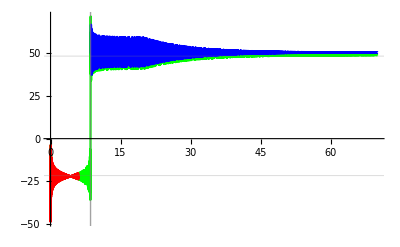

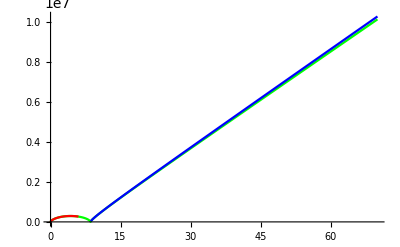

```mathematica
(* Energy *)
Show[
Plot[
(wfunc[x[ta],z[ta],x'[ta],z'[ta]]/.Append[sol,ta->(t*au["ns"])])/au["GHz"],
{t,tlims[[1]]/au["ns"],tlims[[2]]/au["ns"]},PlotRange->All,PlotStyle->Green],
Plot[
(wfunc[x[ta],z[ta],x'[ta],z'[ta]]/.Append[sol1,ta->(t*au["ns"])])/au["GHz"],
{t,tlims1[[1]]/au["ns"],tlims1[[2]]/au["ns"]},PlotRange->All,PlotStyle->Red],
Plot[
(wfunc[x[ta],z[ta],x'[ta],z'[ta]]/.Append[sol2,ta->(t*au["ns"])])/au["GHz"],
{t,tlims2[[1]]/au["ns"],tlims2[[2]]/au["ns"]},PlotRange->All,PlotStyle->Blue](**),
PlotRange->All,GridLines->gridlines]
(* Radius *)
Show[
Plot[rfunc[x[ta],z[ta]]/.Append[sol,ta->t*au["ns"]],{t,tlims[[1]]/au["ns"],tlims[[2]]/au["ns"]},PlotRange->{{tlims[[1]],tlims[[2]]}/au["ns"],All},PlotStyle->Green],Plot[rfunc[x[ta],z[ta]]/.Append[sol1,ta->t*au["ns"]],{t,tlims1[[1]]/au["ns"],tlims1[[2]]/au["ns"]},PlotRange->{{tlims[[1]],tlims[[2]]}/au["ns"],All},PlotStyle->Red],
Plot[rfunc[x[ta],z[ta]]/.Append[sol2,ta->t*au["ns"]],{t,tlims2[[1]]/au["ns"],tlims2[[2]]/au["ns"]},PlotRange->{{tlims[[1]],tlims[[2]]}/au["ns"],All},PlotStyle->Blue]
]
```

## Test Case 3 with Field

### Settings

```mathematica
(* IC *)
w0=-28*au["GHz"];
l0=√(3*(3+1));
θLRL=0;
dL=1;
(* Field parameters *)
fpulse=10*0.72*au["mVcm"];
fmw=4*1000*au["mVcm"];
ω=2*π*15.9/au["ns"];
α=4π/6;
(* timing *)
toff=20*au["ns"];
τring=10*au["ns"];
t0=0;
tmax=toff+5*τring;
(* Getting ic for the solver *)
{x0,z0,vx0,vz0}=icstarting[w0,l0,θLRL,dL];
(* Packaging *)
ic={x0,z0,vx0,vz0};
fields={fpulse,fmw,ω,α};
timing={toff,τring,t0,tmax};
```

### Evaluation

```mathematica
soldata=EvaluationData[solver[ic,fields,timing]];
sol=soldata["Result"][[1]];
tlims=sol[[1,2]]["Domain"][[1]];
ts=FindMinimum[rfunc[x[t],z[t]]/.sol,{t,5.233*au["ns"]}][[2,1,2]];
qr=QuotientRemainder[ts*ω+α+π/2,π]; (* Q is # of periods, R is radians away from ϕ=0 *)
tminus=ts-(2π+qr[[2]])/ω;
tplus=ts+(2π+(π-qr[[2]]))/ω;
style={Red,Thick};
wplus=wfunc[x[t],z[t],x'[t],z'[t]]/.Append[sol,t->tplus];
wminus=wfunc[x[t],z[t],x'[t],z'[t]]/.Append[sol,t->tminus];
gridlines={{{ts/au["ns"],style},{ts/au["ns"]-2π/(ω*au["ns"]),style},{tminus/au["ns"],style},{ts/au["ns"]+2π/(ω*au["ns"]),style},{tplus/au["ns"],style}},{{wplus/au["GHz"],style},{wminus/au["GHz"],style}}};
(* First Segment *)
timing1=Join[timing[[{1,2}]],{0,ts}];
soldata1=EvaluationData[solver[ic,fields,timing1]];
sol1=soldata1["Result"][[1]];
(* Timing *)
{ts1,tminus1,tplus1}=timeskip[sol1,fields];
(* tlims1=sol1[[1,2]]["Domain"][[1]]; *)
(* Translate Initial Conditions *)
xf=x[tminus1]/.sol1;
zf=z[tminus1]/.sol1;
vxf=x'[tminus1]/.sol1;
vzf=z'[tminus1]/.sol1;
bc={xf,zf,vxf,vzf};
(* Timing *)
(* ts1=sol1[[1,2]]["Domain"][[1,2]] *)
timing2=Join[timing[[{1,2}]],{tplus1,tmax}];
ic2=icskip[bc,fields,timing2,ts1,θLRL];
soldata2=EvaluationData[solver[ic2,fields,timing2]];
sol2=soldata2["Result"][[1]];
tlims2=sol2[[1,2]]["Domain"][[1]];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

### Plotting

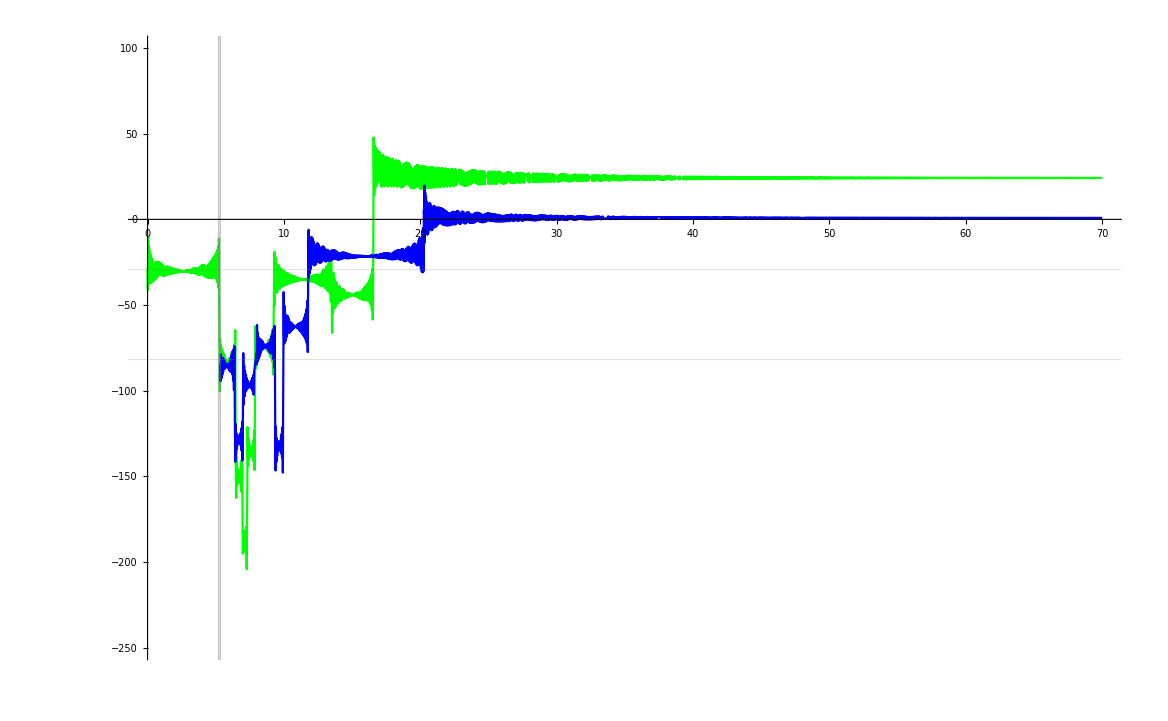

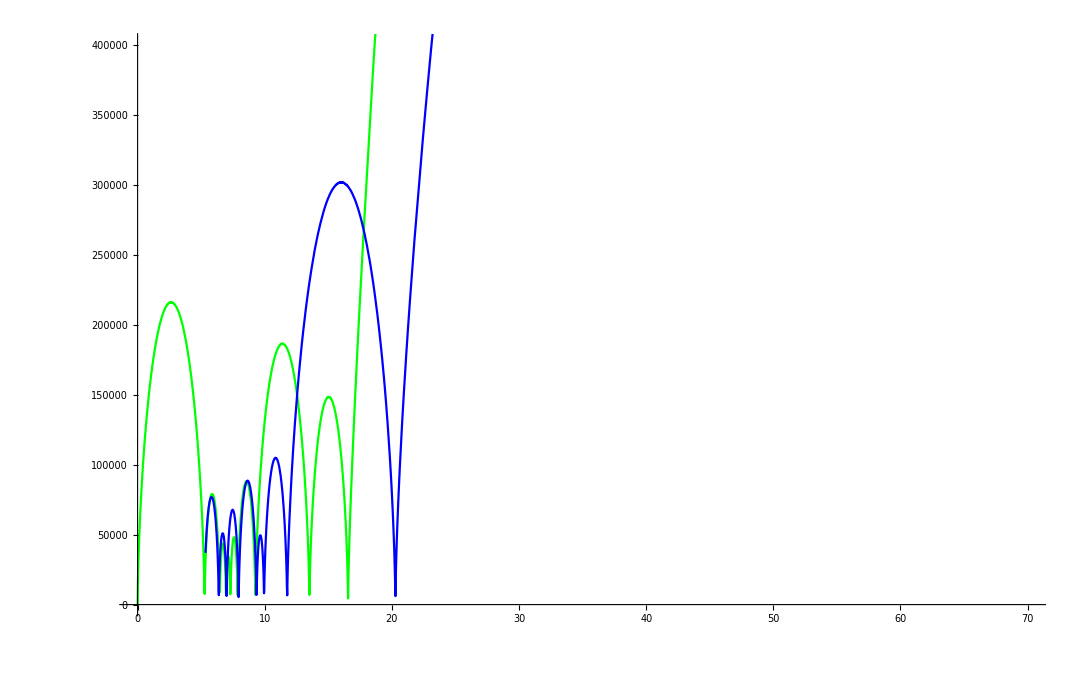

```mathematica
(* Energy *)
Show[
Plot[
(wfunc[x[ta],z[ta],x'[ta],z'[ta]]/.Append[sol,ta->(t*au["ns"])])/au["GHz"],
{t,tlims[[1]]/au["ns"],tlims[[2]]/au["ns"]},PlotRange->All,PlotStyle->Green],
Plot[
(wfunc[x[ta],z[ta],x'[ta],z'[ta]]/.Append[sol1,ta->(t*au["ns"])])/au["GHz"],
{t,tlims1[[1]]/au["ns"],tlims1[[2]]/au["ns"]},PlotRange->All,PlotStyle->Red],
Plot[
(wfunc[x[ta],z[ta],x'[ta],z'[ta]]/.Append[sol2,ta->(t*au["ns"])])/au["GHz"],
{t,tlims2[[1]]/au["ns"],tlims2[[2]]/au["ns"]},PlotRange->All,PlotStyle->Blue],
PlotRange->{All,{-250,100}},GridLines->gridlines]
(* Radius *)
Show[
Plot[rfunc[x[ta],z[ta]]/.Append[sol,ta->t*au["ns"]],{t,tlims[[1]]/au["ns"],tlims[[2]]/au["ns"]},PlotRange->{{tlims[[1]],tlims[[2]]}/au["ns"],All},PlotStyle->Green],
Plot[rfunc[x[ta],z[ta]]/.Append[sol1,ta->t*au["ns"]],{t,tlims1[[1]]/au["ns"],tlims1[[2]]/au["ns"]},PlotRange->{{tlims[[1]],tlims[[2]]}/au["ns"],All},PlotStyle->Red],
Plot[rfunc[x[ta],z[ta]]/.Append[sol2,ta->t*au["ns"]],{t,tlims2[[1]]/au["ns"],tlims2[[2]]/au["ns"]},PlotRange->{{tlims[[1]],tlims[[2]]}/au["ns"],All},PlotStyle->Blue],
PlotRange->{All,{0,4*10^5}}]
```

## Test Case 4 with Field

### Settings

```mathematica
(* IC *)
w0=-28*au["GHz"];
l0=√(3*(3+1));
θLRL=π;
dL=1;
(* Field parameters *)
fpulse=4*0.72*au["mVcm"];
fmw=4*1000*au["mVcm"];
ω=2*π*15.9/au["ns"];
α=4π/6;
(* timing *)
toff=20*au["ns"];
τring=10*au["ns"];
t0=0;
tmax=toff+5*τring;
(* Getting ic for the solver *)
{x0,z0,vx0,vz0}=icstarting[w0,l0,θLRL,dL];
(* Packaging *)
ic={x0,z0,vx0,vz0};
fields={fpulse,fmw,ω,α};
timing={toff,τring,t0,tmax};
```

### Evaluation

```mathematica
soldata=EvaluationData[solver[ic,fields,timing]];
sol=soldata["Result"][[1]];
tlims=sol[[1,2]]["Domain"][[1]];
ts=FindMinimum[rfunc[x[t],z[t]]/.sol,{t,5.233*au["ns"]}][[2,1,2]];
qr=QuotientRemainder[ts*ω+α+π/2,π]; (* Q is # of periods, R is radians away from ϕ=0 *)
tminus=ts-(2π+qr[[2]])/ω;
tplus=ts+(2π+(π-qr[[2]]))/ω;
style={Red,Thick};
wplus=wfunc[x[t],z[t],x'[t],z'[t]]/.Append[sol,t->tplus];
wminus=wfunc[x[t],z[t],x'[t],z'[t]]/.Append[sol,t->tminus];
gridlines={{{ts/au["ns"],style},{ts/au["ns"]-2π/(ω*au["ns"]),style},{tminus/au["ns"],style},{ts/au["ns"]+2π/(ω*au["ns"]),style},{tplus/au["ns"],style}},{{wplus/au["GHz"],style},{wminus/au["GHz"],style}}};
(* First Segment *)
timing1=Join[timing[[{1,2}]],{0,ts}];
soldata1=EvaluationData[solver[ic,fields,timing1]];
sol1=soldata1["Result"][[1]];
(* Timing *)
{ts1,tminus1,tplus1}=timeskip[sol1,fields];
(* tlims1=sol1[[1,2]]["Domain"][[1]]; *)
(* Translate Initial Conditions *)
xf=x[tminus1]/.sol1;
zf=z[tminus1]/.sol1;
vxf=x'[tminus1]/.sol1;
vzf=z'[tminus1]/.sol1;
bc={xf,zf,vxf,vzf};
(* Timing *)
(* ts1=sol1[[1,2]]["Domain"][[1,2]] *)
timing2=Join[timing[[{1,2}]],{tplus1,tmax}];
ic2=icskip[bc,fields,timing2,ts1,θLRL];
soldata2=EvaluationData[solver[ic2,fields,timing2]];
sol2=soldata2["Result"][[1]];
tlims2=sol2[[1,2]]["Domain"][[1]];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

### Plotting

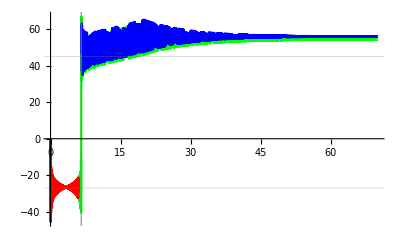

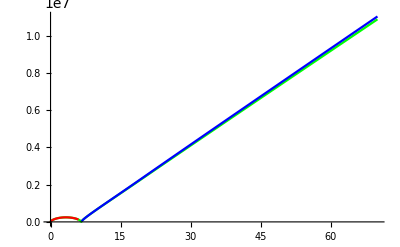

```mathematica
(* Energy *)
Show[
Plot[
(wfunc[x[ta],z[ta],x'[ta],z'[ta]]/.Append[sol,ta->(t*au["ns"])])/au["GHz"],
{t,tlims[[1]]/au["ns"],tlims[[2]]/au["ns"]},PlotRange->All,PlotStyle->Green],
Plot[
(wfunc[x[ta],z[ta],x'[ta],z'[ta]]/.Append[sol1,ta->(t*au["ns"])])/au["GHz"],
{t,tlims1[[1]]/au["ns"],tlims1[[2]]/au["ns"]},PlotRange->All,PlotStyle->Red],
Plot[
(wfunc[x[ta],z[ta],x'[ta],z'[ta]]/.Append[sol2,ta->(t*au["ns"])])/au["GHz"],
{t,tlims2[[1]]/au["ns"],tlims2[[2]]/au["ns"]},PlotRange->All,PlotStyle->Blue],
PlotRange->All,GridLines->gridlines]
(* Radius *)
Show[
Plot[rfunc[x[ta],z[ta]]/.Append[sol,ta->t*au["ns"]],{t,tlims[[1]]/au["ns"],tlims[[2]]/au["ns"]},PlotRange->{{tlims[[1]],tlims[[2]]}/au["ns"],All},PlotStyle->Green],
Plot[rfunc[x[ta],z[ta]]/.Append[sol1,ta->t*au["ns"]],{t,tlims1[[1]]/au["ns"],tlims1[[2]]/au["ns"]},PlotRange->{{tlims[[1]],tlims[[2]]}/au["ns"],All},PlotStyle->Red],
Plot[rfunc[x[ta],z[ta]]/.Append[sol2,ta->t*au["ns"]],{t,tlims2[[1]]/au["ns"],tlims2[[2]]/au["ns"]},PlotRange->{{tlims[[1]],tlims[[2]]}/au["ns"],All},PlotStyle->Blue],
PlotRange->All]
```

```mathematica
(* IC *)
w0=-28*au["GHz"];
l0=√(3*(3+1));
θLRL=0;
dL=1;
(* Field parameters *)
fpulse=0*0.72*au["mVcm"];
fmw=4*1000*au["mVcm"];
ω=2*π*15.9/au["ns"];
α=4π/6;
(* timing *)
toff=20*au["ns"];
τring=10*au["ns"];
t0=0;
tmax=toff+5*τring;
(* Getting ic for the solver *)
{x0,z0,vx0,vz0}=icstarting[w0,l0,θLRL,dL];
(* Packaging *)
ic={x0,z0,vx0,vz0};
fields={fpulse,fmw,ω,α};
timing={toff,τring,t0,tmax};
```

## Test Case with Step Size Error (index=30062 in ErrorMessages.txt)

### Settings

```mathematica
(* IC *)
w0=-20*au["GHz"];
l0=√(3*(3+1));
θLRL=0;
dL=1;
(* Field parameters *)
fpulse=360*0.72*au["mVcm"];
fmw=4*1000*au["mVcm"];
ω=2*π*15.9/au["ns"];
α=62π/100;
(* timing *)
toff=20*au["ns"];
τring=10*au["ns"];
t0=0;
tmax=toff+5*τring;
(* Getting ic for the solver *)
{x0,z0,vx0,vz0}=icstarting[w0,l0,θLRL,dL];
(* Packaging *)
ic={x0,z0,vx0,vz0};
fields={fpulse,fmw,ω,α};
timing={toff,τring,t0,tmax};
```

```mathematica
timing
```

{8.26827×10^8,4.13414×10^8,0,2.8939×10^9}

### First Evaluation

```mathematica
soldata=EvaluationData[solver[ic,fields,timing]];
```

NDSolve::ndsz: At t == 5.66503×10^8, step size is effectively zero; singularity or stiff system suspected.

{5.66503×10^8,5.62763×10^8,5.69263×10^8}

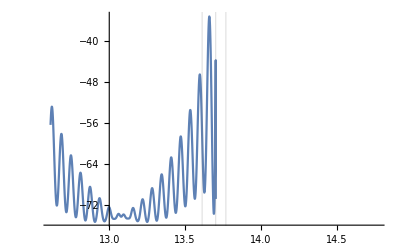

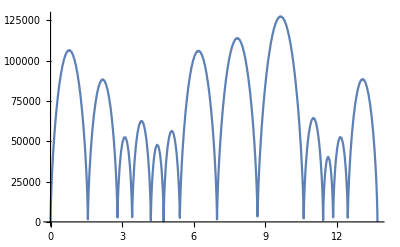

```mathematica
sol=soldata["Result"][[1]];
tlims=sol[[1,2]]["Domain"][[1]];
{ts,tminus,tplus}=timeskip[sol,fields]
Plot[1/au["GHz"]*wfunc[x[ta],z[ta],x'[ta],z'[ta]]/.Append[sol,ta->t*au["ns"]],{t,tminus/au["ns"]-1,tlims[[2]]/au["ns"]},GridLines->{{ts,tminus,tplus}/au["ns"],{}},PlotRange->{{tminus/au["ns"]-1,tplus/au["ns"]+1},All}]
Plot[rfunc[x[ta],z[ta]]/.Append[sol,ta->t*au["ns"]],{t,tlims[[1]]/au["ns"],tlims[[2]]/au["ns"]}]
```

### Second Evaluation

```mathematica
(* IC *)
w0=-20*au["GHz"];
l0=√(3*(3+1));
θLRL=0;
dL=1;
(* Field parameters *)
fpulse=360*0.72*au["mVcm"];
fmw=4*1000*au["mVcm"];
ω=2*π*15.9/au["ns"];
α=62π/100;
(* timing *)
toff=20*au["ns"];
τring=10*au["ns"];
t0=0;
tmax=toff+5*τring;
(* Getting ic for the solver *)
(* {x0,z0,vx0,vz0}=icstarting[w0,l0,θLRL,dL]; *)
(* Packaging *)
ic=icstarting[w0,l0,θLRL,dL];
fields={fpulse,fmw,ω,α};
timing={toff,τring,t0,tmax};
(* First Solve *)
soldata=EvaluationData[solver[ic,fields,timing]];
(* Pull out solution *)
sol=soldata["Result"][[1]];
(* Get time domain limits *)
tlims=sol[[1,2]]["Domain"][[1]];
(* Check for Error *)
errmess=If[soldata["Success"]==False,soldata["MessagesExpressions"][[1,1,1,2]],"NOERR"];
(* Get start and stop times *)
{ts,tminus,tplus}=timeskip[sol,fields];
(* Timing *)
timing2=Join[timing[[{1,2}]],{tplus,tmax}];
(* Translate Initial Conditions *)
bc=fcskip[sol,tminus];
ic2=icskip[bc,fields,timing2,ts,θLRL];
(* Second Solution *)
soldata2=EvaluationData[solver[ic2,fields,timing2]];
(* Get Solution *)
sol2=soldata2["Result"][[1]];
(* Get Limits *)
tlims2=sol2[[1,2]]["Domain"][[1]];
```

NDSolve::ndsz: At t == 5.66503×10^8, step size is effectively zero; singularity or stiff system suspected.

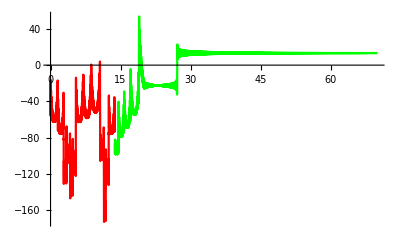

```mathematica
(* Plot Engergy and Radius, 1->Red 2->Green *)
Show[
Plot[1/au["GHz"]*wfunc[x[ta],z[ta],x'[ta],z'[ta]]/.Append[sol,ta->t*au["ns"]],{t,tlims[[1]]/au["ns"],tlims[[2]]/au["ns"]},PlotStyle->Red],
Plot[1/au["GHz"]*wfunc[x[ta],z[ta],x'[ta],z'[ta]]/.Append[sol2,ta->t*au["ns"]],{t,tlims2[[1]]/au["ns"],tlims2[[2]]/au["ns"]},PlotStyle->Green],
PlotRange->All]
Show[
Plot[rfunc[x[ta],z[ta]]/.Append[sol,ta->t*au["ns"]],{t,tlims[[1]]/au["ns"],tlims[[2]]/au["ns"]},PlotStyle->Red],
Plot[rfunc[x[ta],z[ta]]/.Append[sol2,ta->t*au["ns"]],{t,tlims2[[1]]/au["ns"],tlims2[[2]]/au["ns"]},PlotStyle->Green],
PlotRange->All]
```

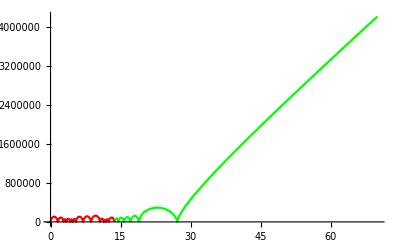

### Plotting

```mathematica
Δw=wslingshot[ts,fields,timing,θLRL];
wplus=wfunc[x[tplus],z[tplus],x'[tplus],z'[tplus]]/.sol2;
wminus=wfunc[x[tminus],z[tminus],x'[tminus],z'[tminus]]/.sol;
gridlines={{tminus,ts,tplus}/au["ns"],{wminus,wplus,wminus+Δw}/au["GHz"]};
```

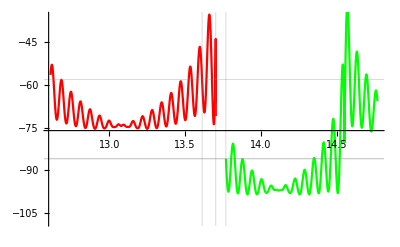

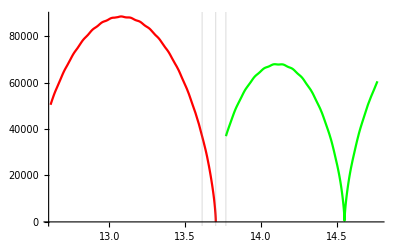

```mathematica
(* Energy *)
Show[
Plot[1/au["GHz"]*wfunc[x[ta],z[ta],x'[ta],z'[ta]]/.Append[sol,ta->t*au["ns"]],{t,tminus/au["ns"]-1,tlims[[2]]/au["ns"]},PlotStyle->Red],
Plot[1/au["GHz"]*wfunc[x[ta],z[ta],x'[ta],z'[ta]]/.Append[sol2,ta->t*au["ns"]],{t,tlims2[[1]]/au["ns"],tplus/au["ns"]+1},PlotStyle->Green],
PlotRange->{{tminus-au["ns"],tplus+au["ns"]}/au["ns"],{wminus-50au["GHz"],wplus+50au["GHz"]}/au["GHz"]},GridLines->gridlines]
(* Radius *)
Show[
Plot[rfunc[x[ta],z[ta]]/.Append[sol,ta->t*au["ns"]],{t,tminus/au["ns"]-1,tlims[[2]]/au["ns"]},PlotStyle->Red],
Plot[rfunc[x[ta],z[ta]]/.Append[sol2,ta->t*au["ns"]],{t,tlims2[[1]]/au["ns"],tplus/au["ns"]+1},PlotStyle->Green],
PlotRange->All,GridLines->{gridlines[[1]],{}}]
```

### Iterating Evaluation

```mathematica
(* IC *)
w0=-20*au["GHz"];
l0=√(3*(3+1));
θLRL=0;
dL=1;
(* Field parameters *)
fpulse=360*0.72*au["mVcm"];
fmw=4*1000*au["mVcm"];
ω=2*π*15.9/au["ns"];
α=62π/100;
(* timing *)
toff=20*au["ns"];
τring=10*au["ns"];
t0=0;
tmax=toff+5*τring;
(* Getting ic for the solver *)
(* {x0,z0,vx0,vz0}=icstarting[w0,l0,θLRL,dL]; *)
(* Packaging *)
ic=icstarting[w0,l0,θLRL,dL];
fields={fpulse,fmw,ω,α};
timing={toff,τring,t0,tmax};
(* First Solve *)
soldata=EvaluationData[solver[ic,fields,timing]];
solutions=Append[{},soldata];
(* Pull out solution *)
sol=soldata["Result"][[1]];
(* Get time domain limits *)
tlims=sol[[1,2]]["Domain"][[1]];
(* Check for Error *)
errmess=If[soldata["Success"]==False,soldata["MessagesExpressions"][[1,1,1,2]],"NOERR"];
(* Iterations *)
n=1;
skips={};
While[errmess=="ndsz",
n=n+1;
Print[n];
(* Get start and stop times *)
{ts,tminus,tplus}=timeskip[sol,fields];
skips=Append[skips,ts];
(* Timing *)
timing=Join[timing[[{1,2}]],{tplus,tmax}];
(* Translate Initial Conditions *)
bc=fcskip[sol,tminus];
ic=icskip[bc,fields,timing,ts,θLRL];
(* Second Solution *)
soldata=EvaluationData[solver[ic2,fields,timing2]];
solutions=Append[solutions,soldata];
(* Get Solution *)
sol=soldata2["Result"][[1]];
(* Get Limits *)
tlims=sol2[[1,2]]["Domain"][[1]];
(* Check for Error *)
errmess=If[soldata["Success"]==False,soldata["MessagesExpressions"][[1,1,1,2]],"NOERR"];
]
```

NDSolve::ndsz: At t == 5.66503×10^8, step size is effectively zero; singularity or stiff system suspected.

2

```mathematica
(* Plotting *)
colors={Red,Green,Orange,Purple,Brown,Blue};
plots={};
Do[
soldata=solutions[[i]];
sol=soldata["Result"][[1]];
tlims=sol[[1,2]]["Domain"][[1]];
plots=Append[
plots,
Plot[1/au["GHz"]*wfunc[x[ta],z[ta],x'[ta],z'[ta]]/.Append[sol,ta->t*au["ns"]],{t,tlims[[1]]/au["ns"],tlims[[2]]/au["ns"]},PlotStyle->{colors[[i]]}]
];
,{i,1,Length[solutions]}];
Show[plots,PlotRange->All,GridLines->{skips,{}}]
```

-Graphics-

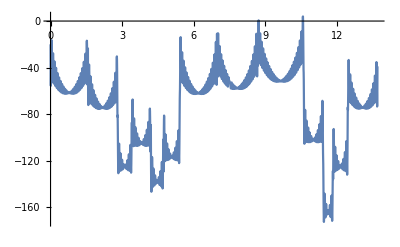
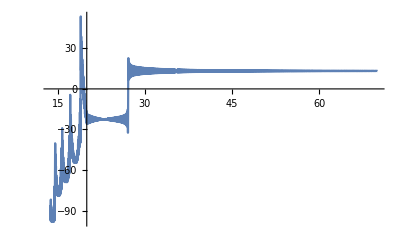

```mathematica
plots
```

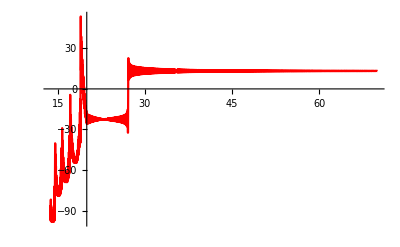

```mathematica
i=1;
Plot[1/au["GHz"]*wfunc[x[ta],z[ta],x'[ta],z'[ta]]/.Append[sol,ta->t*au["ns"]],{t,tlims[[1]]/au["ns"],tlims[[2]]/au["ns"]},PlotStyle->Red]
```

## Test Case with Step Size Error (index=30197 in ErrorMessages.txt)

### Iterating Evaluation

```mathematica
(* Atomic Units *)
au=Association["GHz"->1.5198299055240202*^-7,"ns"->4.134137333656135*^7,"mVcm"->1.9446904672354545*^-13];

(* Solver and Helpers *)
solver=Function[
{ic,fields,timing}, (* ic, fields, timing *)
(* A solver based only on initial conditions,physical conditions and start and stop times. *)
Module[{sol,x0,z0,vx0,vz0,fpulse,fmw,ω,α,toff,τring,t0,tmax},
ClearAll[x,z,t];
(* Unpack *)
{x0,z0,vx0,vz0}=ic;
{fpulse,fmw,ω,α}=fields;
{toff,τring,t0,tmax}=timing;
(* solve *)
sol=NDSolve[
{
x''[t]==-x[t]/(x[t]^2+z[t]^2)^(3/2), (* -r/r^3 *)
x'[t0]==vx0,
x[t0]==x0,
z''[t]==-z[t]/(x[t]^2+z[t]^2)^(3/2) (* -r/r^3 *)
-fpulse*If[t<toff,1,0] (* Field that switches off *)
-fmw*Sin[ω*t+α]*If[t<toff,1,E^(-(t-toff)/τring)], (* MW that rings down *)
z'[t0]==vz0,
z[t0]==z0
},
{x,z},{t,t0,tmax},AccuracyGoal->13,PrecisionGoal->13,MaxSteps->1000000
];
(* return *)
sol]
];

icstarting=Function[
{w0,l0,θLRL,dL},
(* For starting the simulation with known energy, angular momentum, orientation, and angular momentum direction *)
(* r0 and v0 from initial energy *)
If[w0==0,
r0=l0^2/2;
v0=2/l0;
,
r0=(-1+√(1+2*w0*l0^2))/(2*w0);
v0=(1+√(1+2*w0*l0^2))/l0;
];
(* Orient r and v based on θLRL and dL *)
x0=r0*Sin[θLRL];
z0=-r0*Cos[θLRL];
vx0=dL*v0*Cos[θLRL];
vz0=dL*v0*Sin[θLRL];
{x0,z0,vx0,vz0}];
icskip=Function[
{bc,fields,timing,ts,θLRL},
Module[{xf,zf,vxf,vzf,fpulse,fmw,ω,α,toff,τring,t0,tmax,xi,zi,wf,Δw,wi,θvf,vi,vxi,vzi},
(* Unpack *)
{xf,zf,vxf,vzf}=bc;
{fpulse,fmw,ω,α}=fields;
{toff,τring,t0,tmax}=timing;
(* Position *)
xi=xf;
zi=zf;
(* Energy *)
wf=wfunc[xf,zf,vxf,vzf];
Δw=wslingshot[ts,fields,timing,θLRL];
wi=wf+Δw;
(* Velocity *)
θvf=ArcTan[vxf,vzf];
vi=√(2*(wi+1/√(xi^2+zi^2)));
{vxi,vzi}={vi*Cos[θvf+π],vi*Sin[θvf+π]};
{xi,zi,vxi,vzi}]
];

timeskip=Function[{sol,fields},
Module[{ts,fpulse,fmw,ω,α},
(* Unpack *)
{fpulse,fmw,ω,α}=fields;
ts=sol[[1,2]]["Domain"][[1,2]];
qr=QuotientRemainder[ts*ω+α+π/2,π]; (* Q is # of periods, R is radians away from ϕ=0 *)
tminus=ts-(2π+qr[[2]])/ω;
tplus=ts+(2π+(π-qr[[2]]))/ω;
{ts,tminus,tplus}]
];

fcskip=Function[{sol,tfinal},
Module[{xf,zf,vxf,vzf},
xf=x[tfinal]/.sol;
zf=z[tfinal]/.sol;
vxf=x'[tfinal]/.sol;
vzf=z'[tfinal]/.sol;
{xf,zf,vxf,vzf}]
];

(* Evaluation Functions *)
wfunc=Function[{x,z,vx,vz},
1/2*(vx^2+vz^2)-1/√(x^2+z^2)];

rfunc=Function[{x,z},
√(x^2+z^2)];

lfunc=Function[{x,z,vx,vz},
z*vx-x*vz];

wslingshot=Function[
{t,fields,timing,θLRL},
Module[{fpulse,fmw,ω,α,toff,τring,t0,tmax,Δw},
{fpulse,fmw,ω,α}=fields;
{toff,τring,t0,tmax}=timing;
Δw=-If[t<toff,1,E^(-(t-toff)/τring)]*Cos[θLRL]*√3*3/2*fmw/ω^(2/3)*Cos[ω*t+α];
(* return *)
Δw]
];

(* IC *)
w0=-20*au["GHz"];
l0=√(3*(3+1));
θLRL=0;
dL=1;
(* Field parameters *)
fpulse=360*0.72*au["mVcm"];
fmw=4*1000*au["mVcm"];
ω=2*π*15.9/au["ns"];
α=197π/100;
(* timing *)
toff=20*au["ns"];
τring=10*au["ns"];
t0=0;
tmax=toff+5*τring;
(* Packaging *)
ic=icstarting[w0,l0,θLRL,dL];
fields={fpulse,fmw,ω,α};
timing={toff,τring,t0,tmax};
(* First Solve *)
soldata=EvaluationData[solver[ic,fields,timing]];
solutions=Append[{},soldata];
(* Pull out solution *)
sol=soldata["Result"][[1]];
(* Get time domain limits and new start/stop times *)
tlims=sol[[1,2]]["Domain"][[1]];
{ts,tminus,tplus}=timeskip[sol,fields];
(* Check for Error *)
errmess=Which[
(soldata["Success"]==False)&&(tminus>tlims[[1]]),soldata["MessagesExpressions"][[1,1,1,2]],
(soldata["Success"]==False)&&(tminus<=tlims[[1]]),"ShortOrb",
soldata["Success"]==True,"NOERR"
];
(* Iterations *)
n=1;
skips={};
While[errmess=="ndsz",
n=n+1;
Print[n];
skips=Append[skips,ts];
(* Timing *)
timing=Join[timing[[{1,2}]],{tplus,tmax}];
(* Translate Initial Conditions *)
bc=fcskip[sol,tminus];
ic=icskip[bc,fields,timing,ts,θLRL];
(* Second Solution *)
soldata=EvaluationData[solver[ic,fields,timing]];
solutions=Append[solutions,soldata];
(* Get Solution *)
sol=soldata["Result"][[1]];
(* Get time domain limits and new start/stop times *)
tlims=sol[[1,2]]["Domain"][[1]];
{ts,tminus,tplus}=timeskip[sol,fields];
(* Check for Error *)
errmess=Which[
(* NDSolve[] fails AND tminus is in bounds *)
(soldata["Success"]==False)&&(tminus>tlims[[1]]),soldata["MessagesExpressions"][[1,1,1,2]],
(* NDSolve[] fails AND tminus is out of bounds *)
(soldata["Success"]==False)&&(tminus<=tlims[[1]]),"ShortOrb",
(* NDSolve[] succeeds *)
soldata["Success"]==True,"NOERR"
];
];
wfinal=Indeterminate;
Which[
errmess=="NOERR",
wfinal=wfunc[x[t],z[t],x'[t],z'[t]]/.Append[sol,t->tlims[[2]]],
errmess=="ShortOrb",
wfinal=wfunc[x[t],z[t],x'[t],z'[t]]/.Append[sol,t->Mean[tlims]]
];
Print["Error :\t",errmess,"\nWfinal =\t",wfinal/au["GHz"]," GHz"]
```

NDSolve::ndsz: At t == 5.88897×10^8, step size is effectively zero; singularity or stiff system suspected.

2

NDSolve::ndsz: At t == 5.92885×10^8, step size is effectively zero; singularity or stiff system suspected.

Error :	ShortOrb
Wfinal =	-385.51 GHz

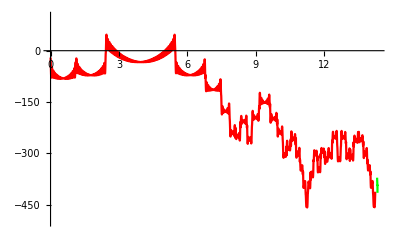

```mathematica
(* Plotting *)
colors={Red,Green,Orange,Purple,Brown,Blue};
plots={};
Do[
soldata=solutions[[i]];
sol=soldata["Result"][[1]];
tlims=sol[[1,2]]["Domain"][[1]];
plots=Append[
plots,
Plot[1/au["GHz"]*wfunc[x[ta],z[ta],x'[ta],z'[ta]]/.Append[sol,ta->t*au["ns"]],{t,tlims[[1]]/au["ns"],tlims[[2]]/au["ns"]},PlotStyle->{colors[[i]]}]
];
,{i,1,Length[solutions]}];
Show[plots,PlotRange->{All,{-500,100}},GridLines->{skips/au["ns"],{}}]
```

## Reading in ErrorMessages.txt

### Read in ErrorConditions.txt and ErrorMessages.txt to Datasets

```mathematica
(* Error Dataset *)
data=Import[FileNameJoin[{NotebookDirectory[],"ErrorMessages.txt"}],"Data"];
headers=data[[1,2;;-1]];
index=data[[2;;-1,1]];
data=data[[2;;-1,2;;-1]];
dataset=Dataset[AssociationThread[index,data]];
dataset=dataset[All,AssociationThread[headers,Range[Length[headers]]]];
dserr=dataset;
(* Conditions Dataset *)
data=Import[FileNameJoin[{NotebookDirectory[],"ErrorConditions.txt"}],"Data"];
headers=data[[1,2;;-1]];
index=data[[2;;-1,1]];
data=data[[2;;-1,2;;-1]];
dataset=Dataset[AssociationThread[index,data]];
dataset=dataset[All,AssociationThread[headers,Range[Length[headers]]]];
dsconds=dataset;
(* list of indicies for each error *)
isz=Keys[dserr[Select[#"Error"=="ndsz"&],"Error"]];
ist=Keys[dserr[Select[#"Error"=="mxst"&],"Error"]];
```

### Run ndsz or mxst error to end

{30196,-3.03966×10^-6,5.04064×10^-11,1,6.15752,0,ShortOrb,3,-0.0000506493}

Runs :	3
Error :	ShortOrb
Wfinal =	-333.256 GHz

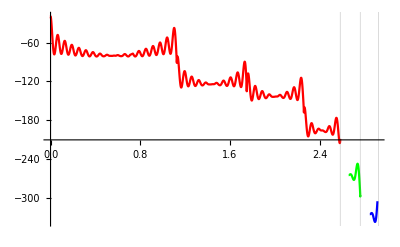

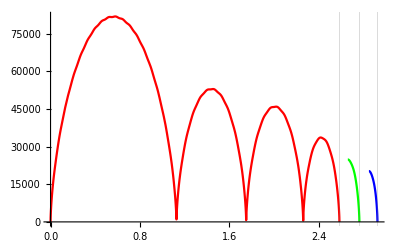

```mathematica
(* Redirect Messages *)
stream=OpenWrite[];
$Messages={stream};

(* Select Conditions *)
i=Key[isz[[-2]]];

(* IC Changing Parameters *)
w0=Round[dsconds[i,"E0"],1]*au["GHz"];
θLRL=Round[dsconds[i,"th_LRL"],1]*π;
dL=Round[dsconds[i,"dL"],1];
fpulse=Round[dsconds[i,"Ep"],0.1]*au["mVcm"];
α=Round[dsconds[i,"phi"],1]*π/100;

(* Complete Solve *)
{solutions,errmess}=completesolve[w0,fpulse,θLRL,dL,α];

(* Output list *)
(* Index, E0, Ep, dL, phi, th_LRL, Error, dlow, dhigh, wfinal *) 
writereport[i,w0,fpulse,dL,α,θLRL,errmess,solutions]

(* Report *)
wfinal=displayreport[solutions,errmess];

(* Reset Messages *)
Close[stream];
$Messages={Streams[[1]]};
```

## Cycle through errors and build report list

```mathematica
(* Conditions Dataset *)
data=Import[FileNameJoin[{NotebookDirectory[],"ErrorConditions.txt"}],"Data"];
headers=data[[1,2;;-1]];
index=data[[2;;-1,1]];
data=data[[2;;-1,2;;-1]];
dataset=Dataset[AssociationThread[index,data]];
dataset=dataset[All,AssociationThread[headers,Range[Length[headers]]]];
dsconds=dataset;
(* list of indicies for each error *)
iall=Keys[dsconds];
(* observation list *)
output={};
(* ParralellDo *)
SetSharedVariable[output];
Monitor[
ParallelDo[
(* Redirect Messages *)
stream=OpenWrite[];
$Messages={stream};
(* Key *)
key=Key[i];
(* IC Changing Parameters *)
w0=Round[dsconds[key,"E0"],1]*au["GHz"];
θLRL=Round[dsconds[key,"th_LRL"],1]*π;
dL=Round[dsconds[key,"dL"],1];
fpulse=Round[dsconds[key,"Ep"],0.1]*au["mVcm"];
α=Round[dsconds[key,"phi"],1]*π/100;
(* Complete Solve *)
{solutions,errmess}=completesolve[w0,fpulse,θLRL,dL,α];
(* Output list *)
(* Index, E0, Ep, dL, phi, th_LRL, Error, dlow, dhigh, wfinal *) 
obs=writereport[key,w0,fpulse,dL,α,θLRL,errmess,solutions];
output=Append[output,obs];
(* Reset Messages *)
Close[stream];
$Messages={Streams[[1]]};
,
{i,Normal[iall]}]
,
{Length[output],Length[iall],ProgressIndicator[Length[output]/5]}]
(* Saving *)
(* {i[[1]],w0,fpulse,dL,N[α],θLRL,errmess,Length[solutions],wfinal} *)
output=Prepend[output,{"","E0","Ep","dL","phi","th_LRL","Error","n","wfinal"}];
fname=FileNameJoin[{NotebookDirectory[],"rewrite.csv"}];
Export[fname,output,"CSV"]
```

C:\Users\labuser\Documents\2D-Comp-Model\computation\rewrite.csv